A simple finite-temperature DMRG code based on TDVP simulation, which recover the left part of fig.2 in Phys. Rev. B 72, 220401 (2005).

Initialize The Notebook

```mathematica
ClearAll["Global`*"];ClearSystemCache[];

(* accuracy control parameters *)
cutoffV=10^-14;cutoffC=10^-14;step=0.01;
bond=10;total=4.;

spin=1/2;d=2;L=64;

sz=DiagonalMatrix@Table[spin-i,{i,0,d-1}];
sp=Block[{table=Table[0,d,d]},Do[table[[i,i+1]]=Sqrt[spin (spin+1)-(spin-(i-1)) (spin-i)],{i,1,d-1}];table];
sm=sp†;
sx=(sp+sm)/2;
sy=(sp-sm)/2/I;
ide=IdentityMatrix@d;
{σx,σy,σz}=2 {sx,sy,sz};so=Table[0,d,d];

supsx=KroneckerProduct[sx,ide];
supsy=KroneckerProduct[sy,ide];
supsp=KroneckerProduct[sp,ide];
supsm=KroneckerProduct[sm,ide];
supsz=KroneckerProduct[sz,ide];
supi=KroneckerProduct[ide,ide];
supo=KroneckerProduct[so,so];
```

Lanczos Method For Krylov Subspace

```mathematica
lanczos[matrix_,vector_,step_,accuV_,accuC_]:=Module[{proxy,vecs={},T,new,expH,c,result,TT,flag=1},
T=SparseArray[{},Dimensions@matrix];
proxy=vector//Normalize;AppendTo[vecs,proxy];T[[1,1]]=Conjugate[proxy].matrix.proxy;
Do[
new=matrix.vecs[[-1]];
new=new-Sum[(Conjugate[vecs[[i]]].new)*vecs[[i]],{i,1,Length@vecs}];
If[(proxy=Norm@new)<accuV,Break[],new=new//Normalize];flag=0;
T[[j,j-1]]=Conjugate[new].matrix.vecs[[-1]];
T[[j-1,j]]=Conjugate[vecs[[-1]]].matrix.new;
T[[j,j]]=Conjugate[new].matrix.new;
TT=SparseArray[step*T[[1;;j,1;;j]]];
AppendTo[vecs,new];expH=MatrixExp@TT;
c=(Transpose@expH)[[1]];
If[Abs[c[[-1]]]<accuC,Break[]];
,{j,2,Length@vector}];
If[flag==1,
result=Exp[step*T[[1,1]]]*vector//Return,
result=Norm[vector]*Sum[c[[i]]*vecs[[i]],{i,1,Length@vecs}]//Return];
];
```

MPS & MPO Functions

```mathematica
MPS;MPO;
initState[]:=(MPS=Table[Null,L,Power[d,2],1,1];)

setState::state="The value `1` is not a vaild state.";
setState::scope="The value `1` should be 1 to `2`.";
setState[po_Integer,state_]:=
(If[po>L||po<1,Message[setState::scope,po,L]];
Switch[state,
(* only valid for case spin-1/2, other cases shoud be modified *)
"UpUp",MPS[[po,1]]={{1}};MPS[[po,2]]={{0}};MPS[[po,3]]={{0}};MPS[[po,4]]={{0}};,
"DnDn",MPS[[po,1]]={{0}};MPS[[po,2]]={{0}};MPS[[po,3]]={{0}};MPS[[po,4]]={{1}};,
"MaxE",MPS[[po,1]]={{1/Sqrt[2]}};MPS[[po,2]]={{0}};MPS[[po,3]]={{0}};MPS[[po,4]]={{1/Sqrt[2]}};,
(* you can define other types of state you like here *)
_,Message[setState::state,state];
];)

checkMPS::dim="The structure of MPS is wrong.";
checkMPS::content="Incomplete definition of MPS.";
checkMPS[]:=(If[Dimensions[MPS]≠{L,Power[d,2],1,1},Message[checkMPS::dim]];
If[MemberQ[Flatten@MPS,Null],Message[checkMPS::content]];)

rightNormalizeMPS[]:=Module[{dims,U,S,V,swap, newbond,norm},
Do[dims=Dimensions[MPS[[i]]];{U,S,V}=SingularValueDecomposition[ArrayReshape[Transpose@MPS[[i]],{dims[[2]],dims[[1]] dims[[3]]}],newbond=Min[dims[[2]],dims[[1]] dims[[3]]]];
MPS[[i]]=Transpose@ArrayReshape[V†,{newbond,dims[[1]],dims[[3]]}];
swap=Activate@TensorContract[Inactive[TensorProduct][MPS[[i-1]],U],{3,4}];MPS[[i-1]]=Activate@TensorContract[Inactive[TensorProduct][swap,S],{3,4}],{i,L,2,-1}];
norm=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[1]],MPS[[1]]],{{3,6},{1,4},{2,5}}];
MPS[[1]]=MPS[[1]]/Sqrt[norm];
];

toMPO[J_]:=((* H = J(σxσx+σyσy+σzσz) *)
MPO=Table[Null,L];
MPO[[1]]={{supo,J supsz,J supsm,J supsp,supi}};
Do[MPO[[i]]={{supi,supo,supo,supo,supo},{supsz,supo,supo,supo,supo},{supsp,supo,supo,supo,supo},{supsm,supo,supo,supo,supo},{supo,J supsz,0.5 J supsm,0.5 J supsp,supi}},{i,2,L-1}];
MPO[[L]]={{supi},{supsz},{supsp},{supsm},{supo}};)

canoShift::direction="Direction should be 'Right' or 'Left'.";
canoShift::scope="The value `1` should be `2` to `3` for `4`.";
canoShift[po_,dir_]:=Module[{proxy,dims,U,S,V,newbond},
dims=Dimensions@MPS[[po]];
Switch[dir,
"Right",(
If[po<1||po≥L,Message[canoShift::scope,po,1,L-1,dir];Break[];];
proxy=ArrayReshape[MPS[[po]],{dims[[1]] dims[[2]],dims[[3]]}];
{U,S,V}=SingularValueDecomposition[proxy,newbond=Min[dims[[1]] dims[[2]],dims[[3]]]];
MPS[[po]]=ArrayReshape[U,{dims[[1]],dims[[2]],newbond}];
MPS[[po+1]]=Activate@TensorContract[Inactive[TensorProduct][S.V†,MPS[[po+1]]],{2,4}]//Transpose;
),
"Left",(
If[po>L||po≤1,Message[canoShift::scope,po,2,L,dir];Break[];];
proxy=ArrayReshape[MPS[[po]]//Transpose,{dims[[2]],dims[[1]] dims[[3]]}];
{U,S,V}=SingularValueDecomposition[proxy,newbond=Min[dims[[2]],dims[[1]] dims[[3]]]];
MPS[[po]]=ArrayReshape[V†,{newbond,dims[[1]],dims[[3]]}]//Transpose;
MPS[[po-1]]=Activate@TensorContract[Inactive[TensorProduct][MPS[[po-1]],U.S],{3,4}];
),
_,Message[canoShift::direction];
];
];

(* Input: (2)--site(1)--site(3)--(4); Output: {MPSL,MPSR} *)
denmatDecomp::direction="Direction should be 'Right' or 'Left'.";
denmatDecomp[psi_,dir_,dims_]:=Module[{U,S,V,pro1,pro2,newbond},
Switch[dir,
"Right",(
{U,S,V}=SingularValueDecomposition[psi,newbond=Min[dims[[1]] dims[[2]],dims[[3]] dims[[4]],bond]];
pro1=ArrayReshape[U,{dims[[1]],dims[[2]],newbond}];
pro2=ArrayReshape[S.V†,{newbond,dims[[3]],dims[[4]]}]//Transpose;
Return@{pro1,pro2};
),
"Left",(
{U,S,V}=SingularValueDecomposition[psi,newbond=Min[dims[[1]] dims[[2]],dims[[3]] dims[[4]],bond]];
pro1=ArrayReshape[U.S,{dims[[1]],dims[[2]],newbond}];
pro2=ArrayReshape[V†,{newbond,dims[[3]],dims[[4]]}]//Transpose;
Return@{pro1,pro2};
),
_,(
Message[denmatDecomp::direction];
newbond=Min[dims[[1]] dims[[2]],dims[[3]] dims[[4]],bond];
pro1=Table[0,dims[[1]],dims[[2]],newbond];
pro2=Table[0,dims[[3]],newbond,dims[[4]]];
Return@{pro1,pro2};
)
];
];

measureEnergy[]:=Module[{eR,proxy},
proxy={{{1}}};
Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[i+1]],proxy],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[i+1]],proxy],{{2,8},{4,5}}];
proxy=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[i+1]],proxy],{{1,5},{3,7}}];
,{i,L-1,0,-1}];
Return[proxy[[1,1,1]]];
];
```

Two-site TDVP Function

```mathematica
twoTDVP[]:=Module[{enL,enR,proxy,Heff,Keff,dims,psi},
enL=Table[Null,L];enR=Table[Null,L];enL[[-1]]={{{1}}};enR[[-1]]={{{1}}};
Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[i+1]],enR[[i+1]]],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[i+1]],proxy],{{2,8},{4,5}}];
enR[[i]]=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[i+1]],proxy],{{1,5},{3,7}}];
,{i,L-1,1,-1}];

(* left end of the chain *)
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[-1]],MPO[[1]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][MPO[[2]],enR[[2]]],{2,6}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,Heff],{3,6}];
Heff=Transpose[Heff,{2,6,1,5,3,7,4,8}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]] dims[[4]],dims[[5]] dims[[6]] dims[[7]] dims[[8]]}];
Heff=(Heff+Heff†)/2.;
psi=Activate@TensorContract[Inactive[TensorProduct][MPS[[1]],MPS[[2]]],{3,5}];
psi=ArrayReshape[psi,Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
{MPS[[1]],MPS[[2]]}=denmatDecomp[psi,"Right",dims[[1;;4]]];
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[-1]],MPS[[1]]],{3,5}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,MPO[[1]]],{{2,5},{3,8}}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,Conjugate@MPS[[1]]],{{4,5},{1,6}}];
enL[[1]]=Transpose[proxy,{3,2,1}];

Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],MPO[[i]]],{2,4}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,enR[[i]]],{3,7}];
Keff=Transpose[proxy,{2,5,1,4,3,6}];dims=Dimensions@Keff;
Keff=ArrayReshape[Keff,{dims[[1]] dims[[2]] dims[[3]],dims[[4]] dims[[5]] dims[[6]]}];
Keff=(Keff+Keff†)/2.;
psi=ArrayReshape[MPS[[i]],Length@Keff];
psi=lanczos[Keff,psi,step/2,cutoffV,cutoffC];
MPS[[i]]=ArrayReshape[psi,{dims[[1]],dims[[2]],dims[[3]]}];
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],MPO[[i]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][MPO[[i+1]],enR[[i+1]]],{2,6}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,Heff],{3,6}];
Heff=Transpose[Heff,{2,6,1,5,3,7,4,8}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]] dims[[4]],dims[[5]] dims[[6]] dims[[7]] dims[[8]]}];
Heff=(Heff+Heff†)/2.;
psi=Activate@TensorContract[Inactive[TensorProduct][MPS[[i]],MPS[[i+1]]],{3,5}];
psi=ArrayReshape[psi,Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
{MPS[[i]],MPS[[i+1]]}=denmatDecomp[psi,"Right",dims[[1;;4]]];
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],MPS[[i]]],{3,5}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,MPO[[i]]],{{2,5},{3,8}}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,Conjugate@MPS[[i]]],{{4,5},{1,6}}];
enL[[i]]=Transpose[proxy,{3,2,1}];
,{i,2,L-1}];

(* right end of the chain *)
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[L-2]],MPO[[L-1]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][MPO[[L]],enR[[L]]],{2,6}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,Heff],{3,6}];
Heff=Transpose[Heff,{2,6,1,5,3,7,4,8}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]] dims[[4]],dims[[5]] dims[[6]] dims[[7]] dims[[8]]}];
Heff=(Heff+Heff†)/2.;
psi=Activate@TensorContract[Inactive[TensorProduct][MPS[[L-1]],MPS[[L]]],{3,5}];
psi=ArrayReshape[psi,Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
{MPS[[L-1]],MPS[[L]]}=denmatDecomp[psi,"Left",dims[[1;;4]]];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[L]],enR[[-1]]],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[L]],proxy],{{2,8},{4,5}}];
enR[[L-1]]=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[L]],proxy],{{1,5},{3,7}}];

Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],MPO[[i]]],{2,4}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,enR[[i]]],{3,7}];
Keff=Transpose[proxy,{2,5,1,4,3,6}];dims=Dimensions@Keff;
Keff=ArrayReshape[Keff,{dims[[1]] dims[[2]] dims[[3]],dims[[4]] dims[[5]] dims[[6]]}];
Keff=(Keff+Keff†)/2.;
psi=ArrayReshape[MPS[[i]],Length@Keff];
psi=lanczos[Keff,psi,step/2,cutoffV,cutoffC];
MPS[[i]]=ArrayReshape[psi,{dims[[1]],dims[[2]],dims[[3]]}];
proxy=Activate@TensorContract[Inactive[TensorProduct][If[i==2,enL[[-1]],enL[[i-2]]],MPO[[i-1]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][MPO[[i]],enR[[i]]],{2,6}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,Heff],{3,6}];
Heff=Transpose[Heff,{2,6,1,5,3,7,4,8}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]] dims[[4]],dims[[5]] dims[[6]] dims[[7]] dims[[8]]}];
Heff=(Heff+Heff†)/2.;
psi=Activate@TensorContract[Inactive[TensorProduct][MPS[[i-1]],MPS[[i]]],{3,5}];
psi=ArrayReshape[psi,Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
{MPS[[i-1]],MPS[[i]]}=denmatDecomp[psi,"Left",dims[[1;;4]]];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[i]],enR[[i]]],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[i]],proxy],{{2,8},{4,5}}];
enR[[i-1]]=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[i]],proxy],{{1,5},{3,7}}];
,{i,L-1,2,-1}];

proxy=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[1]],MPS[[1]]],{{3,6},{1,4},{2,5}}];
MPS[[1]]=MPS[[1]]/Sqrt[proxy];
];
```

One-site TDVP Function

```mathematica
oneTDVP[]:=Module[{enL,enR,proxy,Heff,Keff,dims,psi,U,S,V,newbond},
enL=Table[Null,L];enR=Table[Null,L];enL[[-1]]={{{1}}};enR[[-1]]={{{1}}};
Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[i+1]],enR[[i+1]]],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[i+1]],proxy],{{2,8},{4,5}}];
enR[[i]]=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[i+1]],proxy],{{1,5},{3,7}}];
,{i,L-1,1,-1}];

(* from left to right *)
Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][If[i==1,enL[[-1]],enL[[i-1]]],MPO[[i]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,enR[[i]]],{3,7}];
Heff=Transpose[Heff,{2,5,1,4,3,6}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]],dims[[4]] dims[[5]] dims[[6]]}];
Heff=(Heff+Heff†)/2.;
psi=ArrayReshape[MPS[[i]],Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]] dims[[2]],dims[[3]]}];
{U,S,V}=SingularValueDecomposition[psi,newbond=Min[dims[[1]] dims[[2]],dims[[3]]]];
MPS[[i]]=ArrayReshape[U,{dims[[1]],dims[[2]],newbond}];
proxy=Activate@TensorContract[Inactive[TensorProduct][If[i==1,enL[[-1]],enL[[i-1]]],MPS[[i]]],{3,5}];
proxy=Activate@TensorContract[Inactive[TensorProduct][proxy,MPO[[i]]],{{2,5},{3,8}}];
enL[[i]]=Transpose[Activate@TensorContract[Inactive[TensorProduct][proxy,Conjugate@MPS[[i]]],{{1,6},{4,5}}],{3,2,1}];
Keff=Activate@TensorContract[Inactive[TensorProduct][enL[[i]],enR[[i]]],{2,5}];
Keff=Transpose[Keff,{1,3,2,4}];dims=Dimensions@Keff;
Keff=ArrayReshape[Keff,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
Keff=(Keff+Keff†)/2.;
psi=ArrayReshape[S.V†,Length@Keff];
psi=lanczos[Keff,psi,step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]],dims[[2]]}];
MPS[[i+1]]=Activate@TensorContract[Inactive[TensorProduct][psi,MPS[[i+1]]],{2,4}]//Transpose;
,{i,1,L-1}];

(* from right to left *)
Do[
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],MPO[[i]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,enR[[i]]],{3,7}];
Heff=Transpose[Heff,{2,5,1,4,3,6}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]],dims[[4]] dims[[5]] dims[[6]]}];
Heff=(Heff+Heff†)/2.;
psi=ArrayReshape[MPS[[i]],Length@Heff];
psi=lanczos[Heff,psi,If[i==L,-step,-step/2],cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]],dims[[2]],dims[[3]]}]//Transpose;dims=Dimensions@psi;
psi=ArrayReshape[psi,{dims[[1]],dims[[2]] dims[[3]]}];
{U,S,V}=SingularValueDecomposition[psi,newbond=Min[dims[[1]],dims[[2]] dims[[3]]]];
MPS[[i]]=ArrayReshape[V†,{newbond,dims[[2]],dims[[3]]}]//Transpose;
proxy=Activate@TensorContract[Inactive[TensorProduct][MPS[[i]],enR[[i]]],{3,6}];
proxy=Activate@TensorContract[Inactive[TensorProduct][MPO[[i]],proxy],{{2,8},{4,5}}];
enR[[i-1]]=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[i]],proxy],{{1,5},{3,7}}];
Keff=Activate@TensorContract[Inactive[TensorProduct][enL[[i-1]],enR[[i-1]]],{2,5}];
Keff=Transpose[Keff,{1,3,2,4}];dims=Dimensions@Keff;
Keff=ArrayReshape[Keff,{dims[[1]] dims[[2]],dims[[3]] dims[[4]]}];
Keff=(Keff+Keff†)/2.;
psi=ArrayReshape[U.S,Length@Keff];
psi=lanczos[Keff,psi,step/2,cutoffV,cutoffC];
psi=ArrayReshape[psi,{dims[[1]],dims[[2]]}];
MPS[[i-1]]=Activate@TensorContract[Inactive[TensorProduct][MPS[[i-1]],psi],{3,4}];
,{i,L,2,-1}];

(* left end of the chain *)
proxy=Activate@TensorContract[Inactive[TensorProduct][enL[[-1]],MPO[[1]]],{2,4}];
Heff=Activate@TensorContract[Inactive[TensorProduct][proxy,enR[[1]]],{3,7}];
Heff=Transpose[Heff,{2,5,1,4,3,6}];dims=Dimensions@Heff;
Heff=ArrayReshape[Heff,{dims[[1]] dims[[2]] dims[[3]],dims[[4]] dims[[5]] dims[[6]]}];
psi=ArrayReshape[MPS[[1]],Length@Heff];
psi=lanczos[Heff,psi,-step/2,cutoffV,cutoffC];
MPS[[1]]=ArrayReshape[psi,{dims[[1]],dims[[2]],dims[[3]]}];

proxy=Activate@TensorContract[Inactive[TensorProduct][Conjugate@MPS[[1]],MPS[[1]]],{{3,6},{1,4},{2,5}}];
MPS[[1]]=MPS[[1]]/Sqrt[proxy];
];
```

Main Part

```mathematica
initState[];
Do[setState[i,"MaxE"],{i,1,L}];
checkMPS[];
toMPO[1.];
```

```mathematica
flag=Ceiling[Log2[bond]/2];
rightNormalizeMPS[];
en={};
Do[
If[sweep≤flag,message=AbsoluteTiming[twoTDVP[]],message=AbsoluteTiming[oneTDVP[]]];
Print[message," The ", sweep,"th sweep!"];
energy=measureEnergy[];AppendTo[en,{1./2/(step*sweep),energy/L}];
,{sweep,1,Ceiling[total/step]}];
```

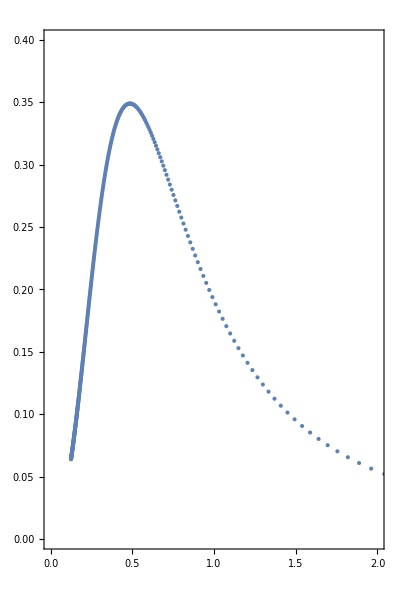

```mathematica
data={};
Do[
swap=en[[i+1]]-en[[i]];
valuey=swap[[2]]/swap[[1]];
valuex=swap[[1]]/2+en[[i,1]];
AppendTo[data,{valuex,valuey}];
,{i,1,Length@en-1}];
ListPlot[data,PlotRange->{{0,2},{0,0.4}},AspectRatio->1.5,Frame->True]
```